```mathematica
Quit[]
```

# Setup

```mathematica
<<SNEG`
```

sneg 1.234 Copyright (C) 2013 Rok Zitko, MODIFIED THE COMMUTATOR AND ANTICOMUTATOR TO BE 2π*δ INSTEAD OF δ

sneg.m $Id: sneg.m,v 1.234 2013/09/24 07:47:24 rokzitko Exp rokzitko $ loaded

```mathematica
<<Mypackage`
```

```mathematica
<<MaTeX`
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{simplewick}"}]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{simplewick}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
ScriptGen[{γ},{1,2,3,4,5}]
```

```mathematica
ψbr[f_,x_,lrntz_:"",clr_:""]/:MakeBoxes[ψbr[f_,x_,lrntz_:"",clr_:""],TraditionalForm]:=SubsuperscriptBox[OverscriptBox[ToBoxes[f,TraditionalForm],StyleBox["_",Bold]],RowBox[{ToBoxes[x,TraditionalForm],ToBoxes[lrntz,TraditionalForm]}],ToBoxes[clr,TraditionalForm]]
```

```mathematica
ψ[f_,x_,lrntz_:"",clr_:""]/:MakeBoxes[ψ[f_,x_,lrntz_:"",clr_:""],TraditionalForm]:=SubsuperscriptBox[ToBoxes[f,TraditionalForm],RowBox[{ToBoxes[x,TraditionalForm],ToBoxes[lrntz,TraditionalForm]}],ToBoxes[clr,TraditionalForm]]
```

```mathematica
WL[z1_,z2_,a_:"",b_:""]/:MakeBoxes[WL[z1_,z2_,a_:"",b_:""],TraditionalForm]:=SubsuperscriptBox["W",RowBox[{ToBoxes[z1,TraditionalForm],";",ToBoxes[z2,TraditionalForm]}],RowBox[{ToBoxes[a,TraditionalForm],ToBoxes[b,TraditionalForm]}]]
```

```mathematica
S[q_,x1_,x2_,lrntz1_:"",lrntz2_:"",clr1_:"",clr2_:""]/:MakeBoxes[S[q_,x1_,x2_,lrntz1_:"",lrntz2_:"",clr1_:"",clr2_:""],TraditionalForm]:=SubsuperscriptBox[RowBox[{"(",SubsuperscriptBox["S",ToBoxes[x1←x2,TraditionalForm],ToBoxes[q,TraditionalForm]],")"}],RowBox[{RowBox[{ToBoxes[lrntz1,TraditionalForm],ToBoxes[lrntz2,TraditionalForm]}]}],RowBox[{ToBoxes[clr1,TraditionalForm],ToBoxes[clr2,TraditionalForm]}]]
```

```mathematica
Sdg[q_,x1_,x2_,lrntz1_:"",lrntz2_:"",clr1_:"",clr2_:""]/:MakeBoxes[Sdg[q_,x1_,x2_,lrntz1_:"",lrntz2_:"",clr1_:"",clr2_:""],TraditionalForm]:=SubsuperscriptBox[SuperscriptBox[RowBox[{"(",SubsuperscriptBox["S",ToBoxes[x1←x2,TraditionalForm],ToBoxes[q,TraditionalForm]],")"}],StyleBox["†",Bold]],RowBox[{RowBox[{ToBoxes[lrntz1,TraditionalForm],ToBoxes[lrntz2,TraditionalForm]}]}],RowBox[{ToBoxes[clr1,TraditionalForm],ToBoxes[clr2,TraditionalForm]}]]
```

```mathematica
(*tt=ψbr[u,f].γ5.ψ[d,f].ψbr[u,x+z].WL[x+z,x].γ3.ψ[u,x].ψbr[u,y].γ2.ψ[u,r].ψ[u,i].γ5.ψbr[d,i]*)
```

```mathematica
OprtrsTeX[Oprtrs_]:=StringReplace[#,"\\overset{\\_}"->"\\overline"]&/@(ToString/@TeXForm/@List@@Oprtrs);
```

```mathematica
Cntrctn2TeX[FldOprtrs_,OPsCntedUnsrt_List]:=Module[{Ops=StringReplace[#,"\\overset{\\_}"->"\\overline"]&/@(ToString/@TeXForm/@List@@FldOprtrs),OPsCnted=Sort/@OPsCntedUnsrt,len=Length[OPsCntedUnsrt],CntedOPs,CntedOPs1,itmp},CntedOPs=Table[Ops⟦#⟧&/@{1;;OPsCnted⟦itmp,1⟧-1,OPsCnted⟦itmp,1⟧;;OPsCnted⟦itmp,1⟧,OPsCnted⟦itmp,1⟧+1;;OPsCnted⟦itmp,2⟧-1,OPsCnted⟦itmp,2⟧;;OPsCnted⟦itmp,2⟧},{itmp,1,len}];CntedOPs1=Table[{(Mod[jtmp,2]*"\\acontraction["+Mod[jtmp+1,2]"\\bcontraction[")<>ToString[IntegerPart[(jtmp+1)/2]]<>"ex]"}~Join~#&[(Map["{"<>StringJoin@@#<>"}"&,CntedOPs,{2}])⟦jtmp⟧],{jtmp,1,len}];StringJoin@@({(StringJoin@@CntedOPs1)<>"  "}~Join~{Ops})]
```

```mathematica
CntndFlds[FldOprtrs_Dot]:=Module[{FldOprtrsLst=List@@FldOprtrs,FrmnFldLst},FrmnFldLst=Union[Select[FldOprtrsLst,MemberQ[{ψ,ψbr},Head[#]]&]//.{ψbr[fld_,___]:>fld,ψ[fld_,___]:>fld}];FrmnFldLst]
```

```mathematica
FndCntrct[FldOprtrs_]:=SortBy[Join@@Module[{itmp,FldOprtrsLst=List@@FldOprtrs,Flds=CntndFlds[FldOprtrs]},Table[SortBy[#,Head[#]]&/@DeleteCases[Subsets[Flatten[Select[FldOprtrsLst,((MemberQ[{ψ,ψbr},Head[#]]&&(#//.{ψbr[fld_,___]:>fld,ψ[fld_,___]:>fld})==Flds⟦itmp⟧)&)]],{2}],_?(Count[#,ψ[_,___]]≠Count[#,ψbr[_,___]]&)],{itmp,1,Length[Flds]}]],First]
```

```mathematica
GrpdCntrctd[FldOprtrs_]:=Module[{OprtrsFnd=FndCntrct[FldOprtrs]},Select[Subsets[SortBy[OprtrsFnd,First],{Length[GroupBy[SortBy[OprtrsFnd,First],First]]}],DuplicateFreeQ[Flatten[#,1]]&]]
```

```mathematica
GrpdCntrctdIndx[FldOprtrs_]:=Module[{OprtrsFnd=FndCntrct[FldOprtrs]},Map[Sort,Map[Position[FldOprtrs,#]⟦1,1⟧&,Select[Subsets[SortBy[OprtrsFnd,First],{Length[GroupBy[SortBy[OprtrsFnd,First],First]]}],DuplicateFreeQ[Flatten[#,1]]&],{3}],2]]
```

```mathematica
ShwCntrctn[FldOprtrs_,nColscale_:{1,2}]:=Module[{indx=GrpdCntrctdIndx[FldOprtrs],lngth},lngth=Length[indx];Grid[ArrayReshape[MaTeX[Cntrctn2TeX[FldOprtrs,#],Magnification->nColscale⟦2⟧]&/@indx,{IntegerPart[lngth/nColscale⟦1⟧]+1,nColscale⟦1⟧},""]]]
```

Convert contraction to propagator ⟨ψ_α^a(y)(ψ̄)_β^b(x)⟩=(S_(y←x))_(α,β)^(a,b)

```mathematica
S[q,y,x,α,β,c,a]
```

(S_(y←x)^q)_αβ^ca

```mathematica
ToPrpgtrs[exp_]:=exp//.{{ψ[q_,x1_,lrntz1_:"",clr1_:""],ψbr[q_,x2_,lrntz2_:"",clr2_:""]}:>S[q,x1,x2,lrntz1,lrntz2,clr1,clr2],{ψbr[q_,x1_,lrntz1_:"",clr1_:""],ψ[q_,x2_,lrntz2_:"",clr2_:""]}:>S[q,x2,x1,lrntz2,lrntz1,clr2,clr1]}
```

```mathematica
CntrctSgn[pairs_]:=Module[{optr,lngth=Length[pairs],optrlst,mom,ncd},snegfermionoperators[optr];optrlst=DeleteCases[Flatten[(SparseArray[Flatten[MapIndexed[{#1⟦1⟧->((optr[First[#2]+1])[AN,mom[First[#2]]]),#1⟦2⟧->((optr[First[#2]+1])[CR,mom[First[#2]]])}&,pairs]]]//Normal)],0];ncd=(nc@@optrlst)//.δ[_]->0;ncd/(ncd//.-x_:>x)]
```

```mathematica
γ5[α_,β_]/:MakeBoxes[γ5[α_,β_],TraditionalForm]:=SubscriptBox[RowBox[{"(",ToBoxes[γ5,TraditionalForm],")"}],RowBox[{ToBoxes[α,TraditionalForm],ToBoxes[β,TraditionalForm]}]]
```

```mathematica
γ3[α_,β_]/:MakeBoxes[γ3[α_,β_],TraditionalForm]:=SubscriptBox[RowBox[{"(",ToBoxes[γ3,TraditionalForm],")"}],RowBox[{ToBoxes[α,TraditionalForm],ToBoxes[β,TraditionalForm]}]]
```

```mathematica
ScriptGen[{α,β,c},{f,i}]
```

```mathematica
Γ[α_,β_]/:MakeBoxes[Γ[α_,β_],TraditionalForm]:=SubscriptBox[RowBox[{"(","Γ",")"}],RowBox[{ToBoxes[α,TraditionalForm],ToBoxes[β,TraditionalForm]}]]
```

```mathematica
Γdg[α_,β_]/:MakeBoxes[Γdg[α_,β_],TraditionalForm]:=SubscriptBox[RowBox[{"(",SuperscriptBox["Γ",StyleBox["†",Bold]],")"}],RowBox[{ToBoxes[α,TraditionalForm],ToBoxes[β,TraditionalForm]}]]
```

```mathematica
P[α_,β_]/:MakeBoxes[P[α_,β_],TraditionalForm]:=SubscriptBox[RowBox[{"(","P",")"}],RowBox[{ToBoxes[α,TraditionalForm],ToBoxes[β,TraditionalForm]}]]
```

# π correlation ⟨(π(f))_α(π^†(i))_α⟩

```mathematica
πOprtrs=ψbr[d,f,αf,cf].γ5[αf,βf].ψ[u,f,βf,cf].ψbr[u,i,αi,ci].γ5[αi,βi].ψ[d,i,βi,ci]
```

(d̄)_(f α_f)^c_f.(γ_5)_(α_f β_f).u_(f β_f)^c_f.(ū)_(i α_i)^c_i.(γ_5)_(α_i β_i).d_(i β_i)^c_i

```mathematica
ShwCntrctn[πOprtrs,{1,1.5}]
```

-Graphics-

```mathematica
πgrphs=GrpdCntrctd[πOprtrs]//.{ψbr[fld_,pos_,___]:>pos,ψ[fld_,pos_,___]:>pos};
```

```mathematica
πgrphs
```

({i,f} | {f,i})

```mathematica
Rule@@#&/@πgrphs⟦1⟧
```

{i→f,f→i}

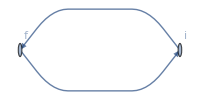

```mathematica
Graph[(Rule@@@πgrphs⟦1⟧),EdgeShapeFunction->({Arrowheads[{{.05,0.5}}],Arrow[Reverse[#]]}&),VertexLabels->"Name",ImageSize->{200,100},AspectRatio->1/2]
```

```mathematica
ToPrpgtrs[GrpdCntrctd[πOprtrs]]
```

((S_(i←f)^d)_(β_i α_f)^(c_i c_f) | (S_(f←i)^u)_(β_f α_i)^(c_f c_i))

```mathematica
πOprtrs
```

(d̄)_(f α_f)^c_f.(γ_5)_(α_f β_f).u_(f β_f)^c_f.(ū)_(i α_i)^c_i.(γ_5)_(α_i β_i).d_(i β_i)^c_i

```mathematica
πrslt=Dot@@Flatten[{γ5[αi,βi]}~Join~ToPrpgtrs[GrpdCntrctd[πOprtrs]]~Join~{γ5[αf,βf]}]
```

(γ_5)_(α_i β_i).(S_(i←f)^d)_(β_i α_f)^(c_i c_f).(S_(f←i)^u)_(β_f α_i)^(c_f c_i).(γ_5)_(α_f β_f)

```mathematica
br[f_]/:MakeBoxes[br[f_],TraditionalForm]:=OverscriptBox[ToBoxes[f,TraditionalForm],"__"]
```

```mathematica
br[d]
```

d^__

```mathematica
πrslt⟦1⟧.πrslt⟦2⟧.πrslt⟦4⟧.πrslt⟦3⟧//.S[q_,i,f,α_,β_,c1_,c2_]:>Sdg[br[q],f,i,α,β,c1,c2]
```

(γ_5)_(α_i β_i).((S_(f←i)^(d^__))^†)_(β_i α_f)^(c_i c_f).(γ_5)_(α_f β_f).(S_(f←i)^u)_(β_f α_i)^(c_f c_i)

```mathematica
CntrctSgn[GrpdCntrctdIndx[πOprtrs]]
```

-1

# Nucleon correlation ⟨(P(f))_α(P^†(i))_α⟩

```mathematica
ϵc[a_,b_,c_]/:MakeBoxes[ϵc[a_,b_,c_],TraditionalForm]:=SuperscriptBox["ϵ",RowBox[ToBoxes[#,TraditionalForm]&/@{a,b,c}]]
```

```mathematica
ScriptGen[{Cγ},{5}]
```

```mathematica
ScriptGen[{i,f}]
```

```mathematica
ScriptGen[{a,b,c,α,β,ρ,μ,ν,γ},{i,f}]
```

```mathematica
NOprtrs=ϵc[af,bf,cf].P[γ,γf].ψ[u,f,γf,af].ψ[u,f1,βf,bf].Γ[βf,αf].ψ[d,f2,αf,cf].ϵc[ai,bi,ci].ψbr[u,i2,αi,ai].Γ[αi,βi].ψbr[d,i1,βi,bi].ψbr[u,i,γi,ci].P[γi,γ]
```

ϵ^(a_f b_f c_f).(P)_(γ γ_f).u_(f γ_f)^a_f.u_(f^1 β_f)^b_f.(Γ)_(β_f α_f).d_(f^2 α_f)^c_f.ϵ^(a_i b_i c_i).(ū)_(i^2 α_i)^a_i.(Γ)_(α_i β_i).(d̄)_(i^1 β_i)^b_i.(ū)_(i γ_i)^c_i.(P)_(γ_i γ)

```mathematica
ShwCntrctn[NOprtrs//.{i1->i,i2->i,f1->f,f2->f},{1,1.5}]
```

-Graphics-
-Graphics-

```mathematica
Ngrphs=GrpdCntrctd[NOprtrs]//.{ψbr[fld_,pos_,___]:>pos,ψ[fld_,pos_,___]:>pos};
```

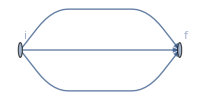

```mathematica
Graph[(Rule@@@Ngrphs⟦1⟧)//.{i1->i,i2->i,f1->f,f2->f},EdgeShapeFunction->({Arrowheads[{{.05,0.5}}],Arrow[Reverse[#]]}&),VertexLabels->"Name",ImageSize->{200,100},AspectRatio->1/2]
```

```mathematica
Graph[(Rule@@@Ngrphs⟦2⟧)//.{i1->i,i2->i,f1->f,f2->f},EdgeShapeFunction->({Arrowheads[{{.05,0.5}}],Arrow[Reverse[#]]}&),VertexLabels->"Name",ImageSize->{200,100},AspectRatio->1/2]
```

-Graphics-

```mathematica
NOprtrs
```

ϵ^(a_f b_f c_f).(P)_(γ γ_f).u_(f γ_f)^a_f.u_(f^1 β_f)^b_f.(Γ)_(β_f α_f).d_(f^2 α_f)^c_f.ϵ^(a_i b_i c_i).(ū)_(i^2 α_i)^a_i.(Γ^†)_(α_i β_i).(d̄)_(i^1 β_i)^b_i.(ū)_(i γ_i)^c_i.(P)_(γ_i γ)

```mathematica
Nrslt1=Times@@Flatten[{ϵc[af,bf,cf],P[γ,γf],ϵc[ai,bi,ci],Γ[αi,βi],Γ[αf,βf],P[γi,γ]}~Join~ToPrpgtrs[GrpdCntrctd[NOprtrs//.{i1->i,i2->i,f1->f,f2->f}]⟦1⟧]];
```

```mathematica
Nrslt2=Times@@Flatten[{ϵc[af,bf,cf],P[γ,γf],ϵc[ai,bi,ci],Γ[αi,βi],Γ[αf,βf],P[γi,γ]}~Join~ToPrpgtrs[GrpdCntrctd[NOprtrs//.{i1->i,i2->i,f1->f,f2->f}]⟦2⟧]];
```

```mathematica
CntrctSgn/@GrpdCntrctdIndx[NOprtrs]
```

{-1,1}

```mathematica
NNcrltr=((-Nrslt1+Nrslt2)//FullSimplify)//.P[α1_,β1_]*P[β1_,γ1_]:>P[α1,γ1]
```

(Γ)_(α_f β_f) (P)_(γ_i γ_f) (Γ)_(α_i β_i) ϵ^(a_f b_f c_f) ϵ^(a_i b_i c_i) (S_(f←i)^d)_(α_f β_i)^(c_f b_i) ((S_(f←i)^u)_(γ_f α_i)^(a_f a_i) (S_(f←i)^u)_(β_f γ_i)^(b_f c_i)-(S_(f←i)^u)_(γ_f γ_i)^(a_f c_i) (S_(f←i)^u)_(β_f α_i)^(b_f a_i))

```mathematica
NNcrltr//.{αf->β',βi->β,cf->b',bi->b,γi->γ,γf->γ',af->c',ci->c,αi->α,βf->α',bf->a',ai->a}//.{Γ[β',α']->-Γ[α',β'],ϵc[c',a',b']->-ϵc[a',b',c']}//FullSimplify
```

(Γ)_αβ (P)_(γ γ') ϵ^abc (Γ)_(α' β') ϵ^(a' b' c') (S_(f←i)^d)_(β' β)^(b' b) ((S_(f←i)^u)_(α' γ)^(a' c) (S_(f←i)^u)_(γ' α)^(c' a)-(S_(f←i)^u)_(α' α)^(a' a) (S_(f←i)^u)_(γ' γ)^(c' c))

# Nucleon correlation ⟨(P(f))_α d(x)Γ d(x)(P^†(i))_α⟩

```mathematica
ScriptGen[{c,η},{1,2}]
```

```mathematica
Δ/:MakeBoxes[Δ[x1_,lrntz1_:"",lrntz2_:"",clr1_:"",clr2_:""],TraditionalForm]:=SubsuperscriptBox[RowBox[{"(",SubscriptBox["Δ",ToBoxes[x1,TraditionalForm]],")"}],RowBox[{RowBox[{ToBoxes[lrntz1,TraditionalForm],ToBoxes[lrntz2,TraditionalForm]}]}],RowBox[{ToBoxes[clr1,TraditionalForm],ToBoxes[clr2,TraditionalForm]}]]
```

```mathematica
Δ[x,η1,η2,c1,c2]
```

(Δ_x)_(η_1 η_2)^(c_1 c_2)

```mathematica
NJNOprtrs=ϵc[af,bf,cf].P[γ,γf].ψ[u,f,γf,af].ψ[u,f1,βf,bf].Γ[βf,αf].ψ[d,f2,αf,cf].ψbr[d,x,η1,c1].Δ[x,η1,η2,c1,c2].ψ[d,x,η2,c2].ϵc[ai,bi,ci].ψbr[u,i2,αi,ai].Γ[αi,βi].ψbr[d,i1,βi,bi].ψbr[u,i,γi,ci].P[γi,γ]
```

ϵ^(a_f b_f c_f).(P)_(γ γ_f).u_(f γ_f)^a_f.u_(f^1 β_f)^b_f.(Γ)_(β_f α_f).d_(f^2 α_f)^c_f.(d̄)_(x η_1)^c_1.(Δ_x)_(η_1 η_2)^(c_1 c_2).d_(x η_2)^c_2.ϵ^(a_i b_i c_i).(ū)_(i^2 α_i)^a_i.(Γ)_(α_i β_i).(d̄)_(i^1 β_i)^b_i.(ū)_(i γ_i)^c_i.(P)_(γ_i γ)

```mathematica
ShwCntrctn[NJNOprtrs//.{i1->i,i2->i,f1->f,f2->f},{1,1.5}]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
NJNgrphs=GrpdCntrctd[NJNOprtrs]//.{ψbr[fld_,pos_,___]:>pos,ψ[fld_,pos_,___]:>pos};
```

```mathematica
NJNgrphs//Length
```

4

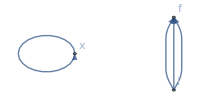

```mathematica
Graph[(Rule@@@NJNgrphs⟦1⟧)//.{i1->i,i2->i,f1->f,f2->f},EdgeShapeFunction->({Arrowheads[{{.05,0.5}}],Arrow[Reverse[#]]}&),VertexLabels->"Name",ImageSize->{200,100},AspectRatio->1/2]
```

```mathematica
Graph[(Rule@@@NJNgrphs⟦2⟧)//.{i1->i,i2->i,f1->f,f2->f},EdgeShapeFunction->({Arrowheads[{{.05,0.5}}],Arrow[Reverse[#]]}&),VertexLabels->"Name",ImageSize->{200,100},AspectRatio->1/2]
```

-Graphics-

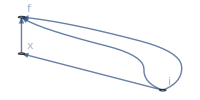

```mathematica
Graph[(Rule@@@NJNgrphs⟦3⟧)//.{i1->i,i2->i,f1->f,f2->f},EdgeShapeFunction->({Arrowheads[{{.05,0.5}}],Arrow[Reverse[#]]}&),VertexLabels->"Name",ImageSize->{200,100},AspectRatio->1/2]
```

```mathematica
Graph[(Rule@@@NJNgrphs⟦4⟧)//.{i1->i,i2->i,f1->f,f2->f},EdgeShapeFunction->({Arrowheads[{{.05,0.5}}],Arrow[Reverse[#]]}&),VertexLabels->"Name",ImageSize->{200,100},AspectRatio->1/2]
```

-Graphics-

```mathematica
NJNOprtrs
```

ϵ^(a_f b_f c_f).(P)_(γ γ_f).u_(f γ_f)^a_f.u_(f^1 β_f)^b_f.(Γ)_(β_f α_f).d_(f^2 α_f)^c_f.(d̄)_(x η_1)^c_1.(Δ_x)_(η_1 η_2)^(c_1 c_2).d_(x η_2)^c_2.ϵ^(a_i b_i c_i).(ū)_(i^2 α_i)^a_i.(Γ)_(α_i β_i).(d̄)_(i^1 β_i)^b_i.(ū)_(i γ_i)^c_i.(P)_(γ_i γ)

```mathematica
NJNrslt1=Times@@Flatten[{ϵc[af,bf,cf],P[γ,γf],ϵc[ai,bi,ci],Γ[αi,βi],Γ[αf,βf],P[γi,γ],Δ[x,η1,η2,c1,c2]}~Join~ToPrpgtrs[GrpdCntrctd[NJNOprtrs//.{i1->i,i2->i,f1->f,f2->f}]⟦3⟧]];
```

```mathematica
NJNrslt2=Times@@Flatten[{ϵc[af,bf,cf],P[γ,γf],ϵc[ai,bi,ci],Γ[αi,βi],Γ[αf,βf],P[γi,γ],Δ[x,η1,η2,c1,c2]}~Join~ToPrpgtrs[GrpdCntrctd[NJNOprtrs//.{i1->i,i2->i,f1->f,f2->f}]⟦4⟧]];
```

```mathematica
(CntrctSgn/@GrpdCntrctdIndx[NJNOprtrs])⟦-2;;-1⟧
```

{-1,1}

```mathematica
NNcrltr=((-NJNrslt1+NJNrslt2)//FullSimplify)//.P[α1_,β1_]*P[β1_,γ1_]:>P[α1,γ1]
```

(Δ_x)_(η_1 η_2)^(c_1 c_2) (Γ)_(α_f β_f) (P)_(γ_i γ_f) (Γ)_(α_i β_i) ϵ^(a_f b_f c_f) ϵ^(a_i b_i c_i) (S_(f←x)^d)_(α_f η_1)^(c_f c_1) (S_(x←i)^d)_(η_2 β_i)^(c_2 b_i) ((S_(f←i)^u)_(γ_f α_i)^(a_f a_i) (S_(f←i)^u)_(β_f γ_i)^(b_f c_i)-(S_(f←i)^u)_(γ_f γ_i)^(a_f c_i) (S_(f←i)^u)_(β_f α_i)^(b_f a_i))

```mathematica
List@@NNcrltr
```

{(P)_(γ_i γ_f),(S_(f←x)^d)_(α_f η_1)^(c_f c_1),(S_(x←i)^d)_(η_2 β_i)^(c_2 b_i),(S_(f←i)^u)_(γ_f α_i)^(a_f a_i) (S_(f←i)^u)_(β_f γ_i)^(b_f c_i)-(S_(f←i)^u)_(γ_f γ_i)^(a_f c_i) (S_(f←i)^u)_(β_f α_i)^(b_f a_i),(Γ)_(α_f β_f),(Γ)_(α_i β_i),(Δ_x)_(η_1 η_2)^(c_1 c_2),ϵ^(a_f b_f c_f),ϵ^(a_i b_i c_i)}

```mathematica
NNcrltr⟦⟧
```

```mathematica
Output Convention
Clear[op,od,Md,M,md,m,ma,Te,δe,ϕp,ϕn]
op/:MakeBoxes[op[a1_,c_,a2_,n_],TraditionalForm]:=SuperscriptBox[SubscriptBox[MakeBoxes[a1,TraditionalForm],RowBox[{MakeBoxes[a2,TraditionalForm],n}]],MakeBoxes[c,TraditionalForm]]
od/:MakeBoxes[od[a1_,c_,a2_,n_],TraditionalForm]:=SuperscriptBox[SubscriptBox[MakeBoxes[a1,TraditionalForm],RowBox[{MakeBoxes[a2,TraditionalForm],n}]],RowBox[{MakeBoxes[c,TraditionalForm],"+"}]]
Md/:MakeBoxes[Md[x1_,x2_,n_],TraditionalForm]:=SuperscriptBox[SubscriptBox[MakeBoxes["M",TraditionalForm],RowBox[{MakeBoxes[x1,TraditionalForm],MakeBoxes[x2,TraditionalForm],n}]],MakeBoxes["+",TraditionalForm]]
M/:MakeBoxes[M[x1_,x2_,n_],TraditionalForm]:=SubscriptBox[MakeBoxes["M",TraditionalForm],RowBox[{MakeBoxes[x1,TraditionalForm],MakeBoxes[x2,TraditionalForm],n}]]
md/:MakeBoxes[md[x1_,x2_,n_],TraditionalForm]:=SuperscriptBox[SubscriptBox[MakeBoxes["m",TraditionalForm],RowBox[{MakeBoxes[x1,TraditionalForm],MakeBoxes[x2,TraditionalForm],n}]],MakeBoxes["+",TraditionalForm]]
m/:MakeBoxes[m[x1_,x2_,n_],TraditionalForm]:=SubscriptBox[MakeBoxes["m",TraditionalForm],RowBox[{MakeBoxes[x1,TraditionalForm],MakeBoxes[x2,TraditionalForm],n}]]
ma/:ma[x1_,x2_,x3_] ma[x4_,x5_,x6_]:=ma[x1.x4,x2,x6]/;x3==x5
ma/:ma[x1_,0,0]:=x1
ma/:ma[x1_,x2_,x3_]:=Tr[x1]/;(x2===x3&&x2=!=0)
Te/:Te[x1_,x2_,x3_] Te[x4_,x5_,x6_]:=KroneckerDelta[x2,x6] KroneckerDelta[x3,x5]/2/;x1==x4
δe/:δe[x1_,x2_]:=N/;x1==x2
ϕp/:MakeBoxes[ϕp[x1_,x2_,x3_],TraditionalForm]:=RowBox[{SubscriptBox[SuperscriptBox["ϕ","+"],MakeBoxes[x1,TraditionalForm]],"(",MakeBoxes[x2,TraditionalForm],",",MakeBoxes[x3,TraditionalForm],")"}]
ϕn/:MakeBoxes[ϕn[x1_,x2_,x3_],TraditionalForm]:=RowBox[{SubscriptBox[SuperscriptBox["ϕ","-"],MakeBoxes[x1,TraditionalForm]],"(",MakeBoxes[x2,TraditionalForm],",",MakeBoxes[x3,TraditionalForm],")"}]
```

Convention Output

```mathematica
(2*λ*Cos[(θ[k]-θ[p])/2]*Cos[(θ[k-Pm]-θ[p-Pm])/2]*ϕn[n,k,Pm]*ϕn[n,p,Pm])/((k-p)^2*Abs[Pm])-(λ*Cos[θ[k]-θ[p]]*ϕn[n,p,Pm]^2)/((k-p)^2*Abs[Pm])-(λ*Cos[θ[k-Pm]-θ[p-Pm]]*ϕn[n,p,Pm]^2)/((k-p)^2*Abs[Pm])+(2*λ*Sin[(θ[k]-θ[p])/2]*Sin[(θ[k-Pm]-θ[p-Pm])/2]*ϕn[n,p,Pm]*ϕp[n,k,Pm])/((k-p)^2*Abs[Pm])+(2*λ*Sin[(θ[k]-θ[p])/2]*Sin[(θ[k-Pm]-θ[p-Pm])/2]*ϕn[n,k,Pm]*ϕp[n,p,Pm])/((k-p)^2*Abs[Pm])+(2*λ*Cos[(θ[k]-θ[p])/2]*Cos[(θ[k-Pm]-θ[p-Pm])/2]*ϕp[n,k,Pm]*ϕp[n,p,Pm])/((k-p)^2*Abs[Pm])-(λ*Cos[θ[k]-θ[p]]*ϕp[n,p,Pm]^2)/((k-p)^2*Abs[Pm])-(λ*Cos[θ[k-Pm]-θ[p-Pm]]*ϕp[n,p,Pm]^2)/((k-p)^2*Abs[Pm])
```

-(λ cos(θ(k)-θ(p)) ((ϕ^-)_n(p,Pm))^2)/(Abs[Pm] (k-p)^2)-(λ ((ϕ^-)_n(p,Pm))^2 cos(θ(k-Pm)-θ(p-Pm)))/(Abs[Pm] (k-p)^2)+(2 λ cos(1/2 (θ(k)-θ(p))) (ϕ^-)_n(k,Pm) (ϕ^-)_n(p,Pm) cos(1/2 (θ(k-Pm)-θ(p-Pm))))/(Abs[Pm] (k-p)^2)-(λ cos(θ(k)-θ(p)) ((ϕ^+)_n(p,Pm))^2)/(Abs[Pm] (k-p)^2)-(λ ((ϕ^+)_n(p,Pm))^2 cos(θ(k-Pm)-θ(p-Pm)))/(Abs[Pm] (k-p)^2)+(2 λ cos(1/2 (θ(k)-θ(p))) (ϕ^+)_n(k,Pm) (ϕ^+)_n(p,Pm) cos(1/2 (θ(k-Pm)-θ(p-Pm))))/(Abs[Pm] (k-p)^2)+(2 λ sin(1/2 (θ(k)-θ(p))) (ϕ^+)_n(k,Pm) (ϕ^-)_n(p,Pm) sin(1/2 (θ(k-Pm)-θ(p-Pm))))/(Abs[Pm] (k-p)^2)+(2 λ sin(1/2 (θ(k)-θ(p))) (ϕ^-)_n(k,Pm) (ϕ^+)_n(p,Pm) sin(1/2 (θ(k-Pm)-θ(p-Pm))))/(Abs[Pm] (k-p)^2)

```mathematica
(m*(Cos[θ[p]]+Cos[θ[p-Pm]])*(ϕn[n,p,Pm]^2+ϕp[n,p,Pm]^2))/Abs[Pm]
```

(m (cos(θ(p))+cos(θ(p-Pm))) (((ϕ^-)_n(p,Pm))^2+((ϕ^+)_n(p,Pm))^2))/Abs[Pm]

```mathematica
((p*Sin[θ[p]]+(p-Pm)*Sin[θ[p-Pm]])*(ϕn[n,p,Pm]^2+ϕp[n,p,Pm]^2))/Abs[Pm]
```

((p sin(θ(p))+(p-Pm) sin(θ(p-Pm))) (((ϕ^-)_n(p,Pm))^2+((ϕ^+)_n(p,Pm))^2))/Abs[Pm]